## Bayes Theorem F. I. Giasemis

### Given information

```mathematica
P[D]=0.001; (* Probability to have the disease. *)
P["+",D]=0.99; (* Probability of True Positive reading. *)
```

### Probability of having the disease, given a positive test result

```mathematica
P[D,"+"]=P["+",D] P[D]/(P["+",D] P[D]+(1-P["+",D])(1-P[D]))
```

0.0901639

### Probability of having the disease, given two positive test results

```mathematica
P[D,"++"]=P["+",D]^2 P[D]/(P["+",D]^2 P[D]+(1-P["+",D])^2(1-P[D]))
```

0.9075

### Probability of having the disease, given n positive test results, in percentage

```mathematica
P[D,"+",n_]:=P["+",D]^n P[D]/(P["+",D]^n P[D]+(1-P["+",D])^n(1-P[D])) *100
```

#### Test

```mathematica
P[D,"+",1]
P[D,"+",2]
P[D,"+",3]
P[D,"+",4]
```

9.01639

90.75

99.8971

99.999

### Given information

```mathematica
P[D]=0.001; (* Probability to have the disease. *)
P["+",D]=0.7; (* Probability of True Positive reading. *)
```

### Probability of having the disease, given n positive test results, in percentage

```mathematica
P[D,"+",n_]:=P["+",D]^n P[D]/(P["+",D]^n P[D]+(1-P["+",D])^n(1-P[D])) *100
```

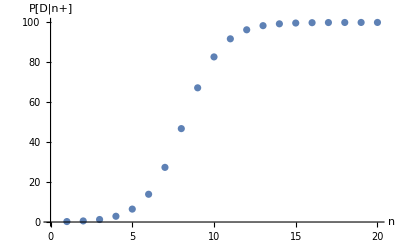

```mathematica
ListPlot[Table[P[D,"+",n],{n,1,20}],AxesLabel->{"n","P[D|n+]"}]
```

```mathematica
P[D,"+",n_,a_]:=a^n P[D]/(a^n P[D]+(1-a)^n(1-P[D])) *100
```

```mathematica
Plot3D[P[D,"+",n,a],{n,1,30},{a,0.55,0.99},AxesLabel->{"n","P[TP]","P[D|n+]"},PlotPoints->100]
```

-Graphics3D-